### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

the_18

{0.111928,0.132629,-0.123497,0.472751,2.77253,-2.25762,0.315494,0.477295,-0.335069,0.918764,0.442627,-0.387979,-0.0864585,-0.12659,-0.109003,2.11973,-0.0832562,0.0563313,-0.561683,0.168499,-1.53454,-1.72487,1.44142,-1.75028,0.789095,1.41907,-1.56809,0.359928,0.993331,0.860212,-1.87618,1.02264,1.77661,-1.29718,-1.05384,0.574407,0.00666913,-0.860212,1.87618,-1.02264,1.65662,-2.19782,-0.200417,0.741622}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

17.2279

-Graphics3D-

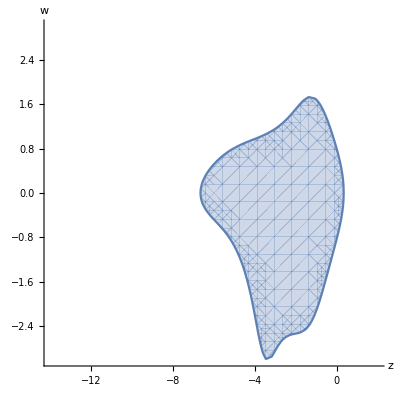

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.11192810076072378,0.13262883029088782,-0.1234974021270067,0.47275148345109247,2.772528043817576,-2.2576237541934234,0.3154940925986448,0.477295386063596,-0.3350693235576111,0.9187638808275728,0.4426271042794905,-0.38797880230105597,-0.08645848450865604,-0.126589728934268,-0.10900264352638281,2.1197307865185193,-0.08325617516361535,0.056331305019829164,-0.5616832951329531,0.16849869218940358,-1.53453579228987,-1.7248659459259568,1.4414202184477871,-1.750279183763761,0.7890950678496153,1.419068280624181,-1.568091709546484,0.3599283412704874,0.993330928446762,0.8602116821903294,-1.876182816848765,1.0226402194167947,1.7766102490175062,-1.29717868642074,-1.053838827477135,0.5744072829345664,0.006669129128692135,-0.8602117394808352,1.876182768602042,-1.022640185231043,1.6566152296290777,-2.1978195692359757,-0.20041743280366192,0.7416220767272357}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

16_low_constraints

{0.0396082,-0.672829,1.10543,-3.18939,3.52242,0.647068,0.238412,0.333677,0.268466,0.589353,0.409034,-0.0210367,0.0474132,1.5244,-0.114598,-0.557673,1.08644,-1.16839,-0.488275,-0.856089,0.300427,-0.844793,-0.36376,0.106773,-1.21203,1.35133,0.725305,0.135402,2.93695,-4.49501,1.14192,1.41614,2.99379,-4.24283,0.55757,0.691468,-1.93695,4.49501,-1.14192,-1.41614,3.4275,-2.37955,-4.24172,3.19377}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

15.9933

-Graphics3D-

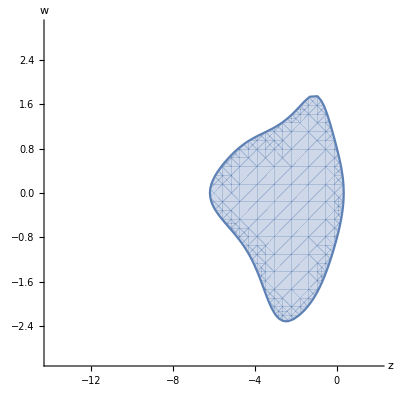

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.03960820870055627,-0.672828570955491,1.105432202163936,-3.1893931350195652,3.5224241323478287,0.6470681370179244,0.23841231178189298,0.3336767631496378,0.2684656286258517,0.5893525876547066,0.409034110106811,-0.021036748842822837,0.04741323039961802,1.5243980102694101,-0.11459835510967661,-0.5576729688500409,1.0864430435810442,-1.168385476894648,-0.48827483227206325,-0.8560892695354937,0.3004273859604081,-0.844793259364066,-0.3637603753973796,0.1067729250337655,-1.212032582518156,1.3513263896652477,0.7253046096818107,0.1354015831709847,2.9369493437354146,-4.495012058553649,1.141917957500433,1.4161447573178414,2.9937905340751128,-4.2428281767811065,0.5575697988805257,0.6914678438246266,-1.936949343736112,4.495012058555196,-1.141917957501083,-1.4161447573180925,3.4275011606744994,-2.3795536381095284,-4.241722511233094,3.1937749886680438}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9038516.comet-31-09

{0.237563,0.167794,-0.167168,0.328209,2.41338,-1.74187,0.224625,0.534632,0.448132,0.295433,0.316959,-0.0121193,-0.012294,0.337358,-0.974525,2.96139,-0.386011,0.519214,-0.473946,-0.793906,-0.354467,0.990121,-2.89037,1.29447,0.18192,1.32403,-0.691898,0.185944,3.05013,-4.79343,1.12421,1.61909,3.0816,-4.38177,0.532813,0.767361,-2.05013,4.79343,-1.12421,-1.61909,3.11923,-1.91132,3.01812,-4.22603}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

15.0402

-Graphics3D-

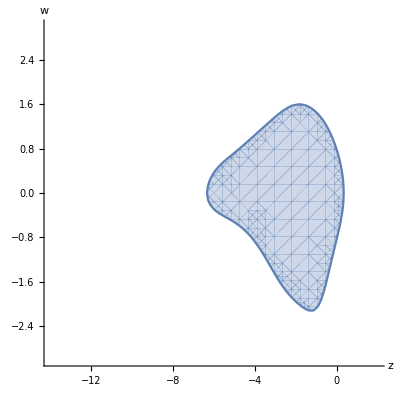

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.2375631448360372,0.1677938050574444,-0.16716753322331462,0.32820945703931464,2.413379273941924,-1.7418729202158048,0.22462511150159892,0.5346321733315803,0.4481317984835585,0.2954330887730655,0.31695870546123667,-0.012119348437104112,-0.012293993837460151,0.33735768605853406,-0.9745253653297667,2.9613903035593054,-0.38601114315351587,0.5192138533536769,-0.47394647263324563,-0.793906144489265,-0.3544671831815408,0.9901211392247707,-2.890371974471287,1.2944661254874494,0.18191972201417064,1.32403393594869,-0.6918981501152758,0.18594449195861704,3.0501314822747885,-4.7934274681607345,1.1242057905178544,1.6190901957827384,3.081595078845567,-4.381769469228848,0.532813365308558,0.7673610228560661,-2.0501314718554013,4.793427451746305,-1.1242057881788357,-1.6190901913447249,3.119230540687771,-1.911323094707116,3.018118420223643,-4.226025866495189}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

#### jOpt.9038509.comet-31-05

{0.391162,0.174539,0.506408,0.0380888,0.626191,0.335705,0.544584,0.969054,0.0290336,0.0456205,0.0797458,-0.12503,1.18692,0.256954,0.208988,2.36291,0.15331,-0.161781,0.737967,-0.00816398,1.99303,-0.20912,1.89314,0.079277,0.14224,0.450716,0.261225,0.145819,1.49068,-0.561082,1.30847,-1.23807,-1.71719,1.76915,-0.965604,0.913645,-0.490679,0.561083,-1.30847,1.23807,1.30448,-2.00672,1.09505,-0.392809}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

18.164

-Graphics3D-

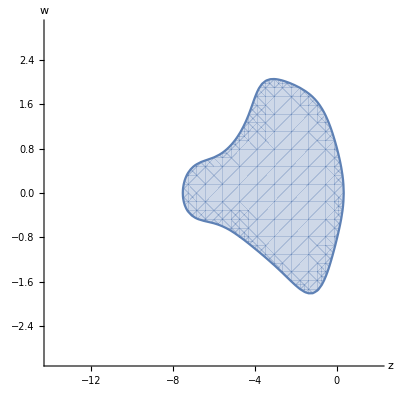

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.3911621956435803,0.1745390695487835,0.5064083441125075,0.038088759939697056,0.6261905207215289,0.33570528442032715,0.5445840776281785,0.9690544187627487,0.029033583268759943,0.04562046801969214,0.07974579905783213,-0.12503000586558607,1.186917036432333,0.25695438158763273,0.20898801997375321,2.362910090835852,0.15331043101491074,-0.16178115455153008,0.7379666561554212,-0.008163978357511743,1.9930330277449437,-0.20912043140603992,1.8931430414617094,0.07927697260910856,0.14224036421230615,0.4507157014002052,0.2612245041422075,0.1458191876930347,1.4906779409656241,-0.5610821369544496,1.3084735298201007,-1.2380695742035914,-1.7171879158908514,1.7691459695740177,-0.9656043542408547,0.9136454098365391,-0.49067861581685,0.5610828577377615,-1.3084746842624968,1.2380707939829407,1.3044757613017526,-2.006718655625648,1.095051636723743,-0.39280919195898817}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9038492.comet-31-04

{0.185612,0.156743,0.46723,2.07411,-0.638777,-1.22355,0.256423,0.472591,0.359032,0.185525,0.674574,-0.105434,0.134504,1.41062,0.423972,0.0952289,0.026886,-0.315114,0.506387,1.02942,-0.736304,-0.409556,1.05022,0.888843,-0.667901,1.31498,0.439557,-0.0866366,1.7859,-2.96821,1.48399,0.698316,-2.37273,3.4778,-0.751454,-0.353612,-0.785908,2.96822,-1.48399,-0.698317,2.56959,-3.88631,0.0371618,1.27955}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

16.8747

-Graphics3D-

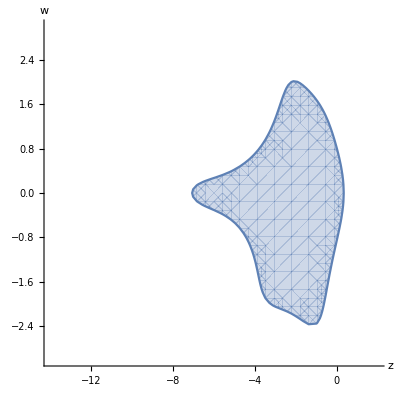

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.18561182061178988,0.15674283895075566,0.4672303190312629,2.0741055723173725,-0.6387771655772243,-1.2235510565189451,0.25642282316651777,0.47259121735943055,0.35903207901953815,0.18552543915723077,0.6745736880485947,-0.1054338807458157,0.1345043564333114,1.4106249004473523,0.4239716276116891,0.09522892018630975,0.026886041013620358,-0.31511397528770035,0.5063869084736877,1.0294218523476466,-0.7363035882548292,-0.4095561579974505,1.0502176549265982,0.8888434571683972,-0.667901456296847,1.31498116012076,0.4395570313506383,-0.08663659256495526,1.7859042248158694,-2.9682118909642,1.4839919390075529,0.6983159337888527,-2.3727286875667986,3.4777953911214263,-0.7514541311778533,-0.3536120260616499,-0.7859084158469182,2.968220324714149,-1.4839944279387123,-0.6983172743047301,2.569592380059495,-3.8863052592187346,0.037161820951290385,1.2795514095567642}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9038478.comet-31-09

{0.0912836,0.0768586,0.167979,-0.869895,0.973982,0.289196,0.361697,-0.631671,0.659282,0.970765,0.027478,-0.0204411,0.111302,0.714492,-0.0225321,-1.77536,0.366606,0.0300486,-0.601413,3.4434,-1.91617,-0.154616,-0.376577,-0.262288,0.0107544,-1.43668,2.17541,0.250517,0.665371,-1.45408,0.234757,1.55395,1.4615,-2.53725,0.141186,0.934565,0.334629,1.45408,-0.234757,-1.55395,-2.79659,3.39733,0.675017,-1.27576}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

14.3967

-Graphics3D-

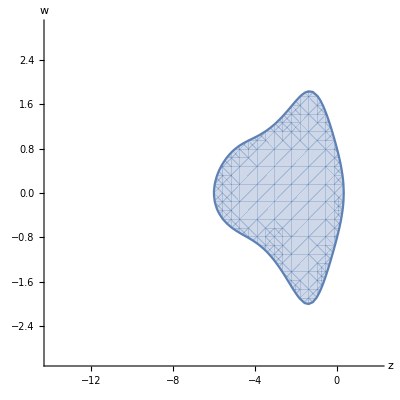

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.09128364464847562,0.07685856231460303,0.16797866589276303,-0.8698954391324083,0.9739819036869254,0.2891960777507126,0.361697418795469,-0.6316711657453554,0.6592821431764943,0.9707647816177337,0.0274779726201939,-0.020441133902321003,0.11130232786029458,0.7144919497704894,-0.02253214883338491,-1.775364189982162,0.36660643905711743,0.03004859688697596,-0.6014126872481393,3.443396915805442,-1.916168298311381,-0.15461551558740327,-0.3765765825449205,-0.2622877933195379,0.010754350714602748,-1.43668225492882,2.175410552157654,0.2505173575822458,0.6653707092903529,-1.4540764583606145,0.23475675659250653,1.5539489896542045,1.4615017942702557,-2.5372528161040577,0.14118567932231746,0.9345653455880429,0.33462927997331776,1.454076476440134,-0.234756755424434,-1.5539490003043341,-2.796585562545305,3.3973325053122934,0.6750172373521466,-1.275764184810692}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```